# Everybody Svasa, let’s try to understand when

```mathematica
thetaWavesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/segnali_belli/Thetacomponent.mat"];
numSamplesTheta= Dimensions[thetaWavesMatlab][[3]];
thetaWavesRaw =  Table[Transpose[thetaWavesMatlab[[1,1,x]]],{x,numSamplesPhasedOxyYes}];
```

```mathematica
Dimensions[thetaWavesRaw]
```

{30,5}

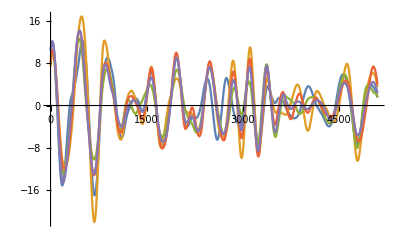

```mathematica
ListLinePlot[thetaWavesRaw[[4]]]
```

```mathematica
meanTheta = Table[Mean[thetaWavesRaw[[x,All]]],{x,30}];
```

```mathematica
Dimensions[meanTheta[[1]]]
```

{5102}

```mathematica
meanThetaStandard={};
If[Dimensions[meanTheta [[#]]][[1]]==5102,AppendTo[meanThetaStandard,Drop[meanTheta [[#]],-1]], AppendTo[meanThetaStandard,meanTheta [[#]]]]&/@Range[numSamplesTheta];
```

```mathematica
Manipulate[ListLinePlot[meanThetaStandard[[Floor@i]]],{i,1,30}]
```

```mathematica
Dimensions[meanThetaStandard]
```

{30,5101}

```mathematica
meanTheta
```

{{-0.179152,-0.111499,-0.0442472,0.0225645,0.0889216,0.154845,0.220332,0.285349,0.349847,0.413737,0.476942,0.539446,0.601217,0.662205,0.722377,5072,-2.70061,-2.65344,-2.60577,-2.5576,-2.50893,-2.4598,-2.41021,-2.36017,-2.30968,-2.25873,-2.20732,-2.15543,-2.10307,-2.0502,-1.99679},28,{1}}
 |  |  |  |

```mathematica
clus = FindClusters[#,Method->"DBSCAN"]&@meanThetaStandard
Dimensions@clus
```

{{{-0.179152,-0.111499,-0.0442472,0.0225645,0.0889216,0.154845,0.220332,5088,-2.30968,-2.25873,-2.20732,-2.15543,-2.10307,-2.0502},26,{1}},1}
 |  |  |  |

{2}

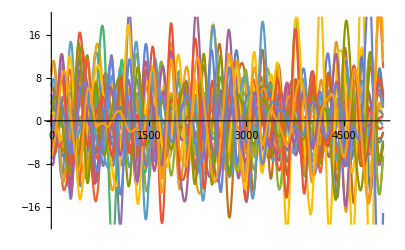
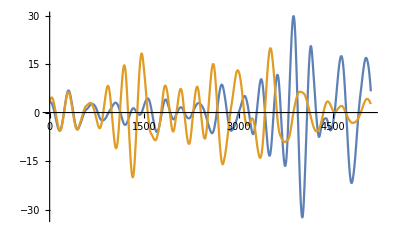

```mathematica
ListLinePlot/@clus
```

```mathematica
clus = FindClusters[#]&@meanThetaStandard
Dimensions@clus
```

1
 |  |  |  |

{2}

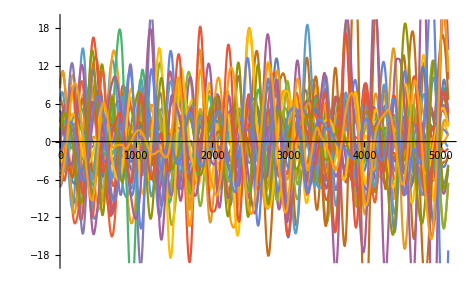
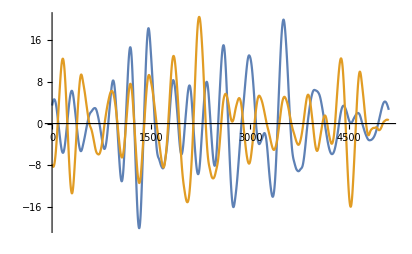

```mathematica
ListLinePlot/@clus
```

{{28,5101},{2,5101}}

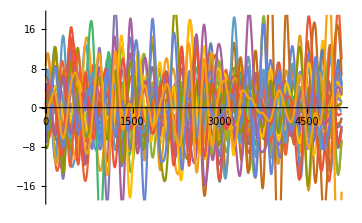
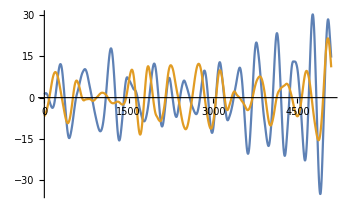

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,26,27,28,29}
{25,30}

```mathematica
clus = FindClusters[meanThetaStandard,2,Method->"KMeans",DistanceFunction->ManhattanDistance];
Dimensions/@clus
ListLinePlot/@clus
clusLabeled = FindClusters[labeledTheta,2,Method->"KMeans",DistanceFunction->ManhattanDistance]//Column
```

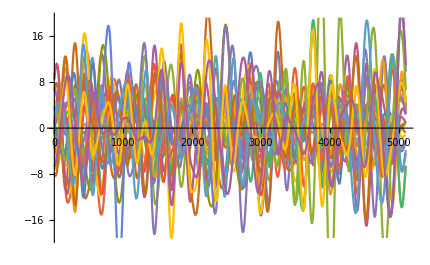
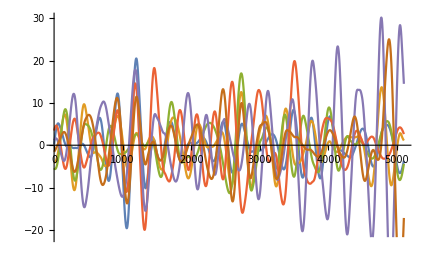

```mathematica
ListLinePlot/@clus
```

```mathematica
Dimensions/@clus
```

{{24,5101},{6,5101}}

```mathematica
24/30//N
```

0.8

```mathematica
labeledTheta = Table[meanThetaStandard[[i]]-> ToString@i,{i,30}];
```

```mathematica
clus = FindClusters[labeledTheta,2,Method->"KMedoids",DistanceFunction->EuclideanDistance]//Column
```

{1,2,3,4,6,7,10,11,12,13,14,15,16,17,18,19,20,21,22,23,26,27,28,30}
{5,8,9,24,25,29}

```mathematica
4/6.
```

0.666667

# Let’s cluster on the mean power and see what happens

```mathematica
Total[Square[
```